```mathematica
<<CustomTicks`
```

```mathematica
tickll=LogTicks[-30,10];
Do[tickll[[i,1]]=10^tickll[[i,1]],{i,1,Length[tickll]}];
tickll;
```

## PDF

```mathematica
(*W/mu pdf*)NLLfWL= (0.002705634032562221*(-1 + x^(-1)))/
     (1 - 0.017135682206227396*(4.512918922923938 - Log[Q]));
(*γ/mu pdf*)NLLfP[x_, Q_] := ((5144.959772459887 + 41.706746184531845*Log[Q] - 
       1.*Log[Q]^2)*((0.23286810520409482*(-0.05019647001236063 + 
          0.050820821453427104/x + 0.025254322866446938*x + 
          0.0006243514410664896*Log[x] - 0.0003121757205332448*x*Log[x] + 
          Log[Q]*(4.475282434709431*^-6 - 1.1188206086773578*^-6*x + 
            (4.475282434709431*^-6 - 2.2376412173547157*^-6*x)*Log[x]) + 
          Log[Q]^3*(2.9954249057675606*^-8 - 7.488562264418902*^-9*x + 
            (2.9954249057675606*^-8 - 1.4977124528837803*^-8*x)*Log[x]) + 
          Log[Q]^5*(2.851344447543248*^-12 - 7.12836111885812*^-13*x + 
            (2.851344447543248*^-12 - 1.425672223771624*^-12*x)*Log[x]) + 
          Log[Q]^7*(6.426035213686277*^-17 - 1.606508803421569*^-17*x + 
            (6.426035213686277*^-17 - 3.213017606843138*^-17*x)*Log[x]) + 
          Log[Q]^9*(8.97112165143488*^-22 - 2.24278041285872*^-22*x + 
            (8.97112165143488*^-22 - 4.48556082571744*^-22*x)*Log[x]) + 
          Log[Q]^10*(-3.498957749738689*^-24 + 8.747394374346723*^-25*x + 
            (-3.498957749738689*^-24 + 1.7494788748693445*^-24*x)*Log[x]) + 
          Log[Q]^8*(-2.321932626668352*^-19 + 5.80483156667088*^-20*x + 
            (-2.321932626668352*^-19 + 1.160966313334176*^-19*x)*Log[x]) + 
          Log[Q]^6*(-1.4158707268552207*^-14 + 3.539676817138052*^-15*x + 
            (-1.4158707268552207*^-14 + 7.079353634276104*^-15*x)*Log[x]) + 
          Log[Q]^4*(-2.9287822611284457*^-10 + 7.321955652821114*^-11*x + 
            (-2.9287822611284457*^-10 + 1.4643911305642229*^-10*x)*Log[x]) + 
          Log[Q]^2*(-6.873099902738211*^-7 + 1.7182749756845527*^-7*x + 
            (-6.873099902738211*^-7 + 3.4365499513691054*^-7*x)*Log[x]) + 
          ArcSin[0.2791683015027376 - 0.013387201210449512*Log[Q]]*
           (0.10568504203410027 - 0.10748615458500281/x - 0.05329279915477576*
             x + (-0.0018011125509025418 + 0.0009005562754512709*x)*Log[x])))/
        (Sqrt[1.0495714523398239 - 0.010984343655725643*Log[Q]]*
         Sqrt[0.9226680555143054 + 0.017135682206227396*Log[Q]]) + 
       (38.78446808702186 - 38.08481866056622*x + 19.217321686897016*x^2 + 
         Log[Q]^2*(-0.00048717779001536285 + 0.0007111582475538456*x - 
           0.00029958400939230213*x^2 + (0.00022398045753848278 - 
             0.00011199022876924139*x)*x*Log[x]) + 
         Log[Q]^3*(-5.142211286111232*^-6 + 5.584712888909655*^-6*x - 
           2.681731043755221*^-6*x^2 + (4.4250160279842256*^-7 - 
             2.2125080139921128*^-7*x)*x*Log[x]) + 
         Log[Q]^4*(-5.419872217505981*^-8 + 7.87026168868856*^-8*x - 
           3.3225334765486354*^-8*x^2 + (2.4503894711825804*^-8 - 
             1.2251947355912902*^-8*x)*x*Log[x]) + 
         Log[Q]^5*(-3.344668177706287*^-10 + 3.8333474581551137*^-10*x - 
           1.7945039089653502*^-10*x^2 + (4.886792804488264*^-11 - 
             2.443396402244132*^-11*x)*x*Log[x]) + 
         Log[Q]^6*(-1.8999287874589977*^-12 + 2.7181824238417466*^-12*x - 
           1.154527802825186*^-12*x^2 + (8.182536363827488*^-13 - 
             4.091268181913744*^-13*x)*x*Log[x]) + 
         Log[Q]^7*(-7.226031665564217*^-15 + 9.353657170489722*^-15*x - 
           4.144922209013484*^-15*x^2 + (2.1276255049255077*^-15 - 
             1.0638127524627539*^-15*x)*x*Log[x]) + 
         Log[Q]^8*(-2.5026152954488565*^-17 + 3.914664312719544*^-17*x - 
           1.6043199020421002*^-17*x^2 + (1.4120490172706877*^-17 - 
             7.060245086353439*^-18*x)*x*Log[x]) + 
         Log[Q]^9*(-5.3092658060748197*^-20 + 7.765958554179628*^-20*x - 
           3.268806090063612*^-20*x^2 + (2.4566927481048075*^-20 - 
             1.2283463740524037*^-20*x)*x*Log[x]) + 
         Log[Q]^10*(-9.450535155605765*^-23 + 2.042356101538346*^-22*x - 
           7.468524042747305*^-23*x^2 + (1.0973025859777693*^-22 - 
             5.486512929888847*^-23*x)*x*Log[x]) + 
         Log[Q]*(0.004732014818197644 - 0.00678978213808091*x + 
           0.0028804492390696384*x^2 + (-0.002057767319883267 + 
             0.0010288836599416334*x)*x*Log[x]) - 8.462148404533865*
          Log[95.55158553262575 - 1.*Log[Q]] + 8.309292186229362*x*
          Log[95.55158553262575 - 1.*Log[Q]] - 4.192860147690808*x^2*
          Log[95.55158553262575 - 1.*Log[Q]] + x*Log[x]*(0.6996494264556375 - 
           0.3498247132278188*x + (-0.15285621830450422 + 0.07642810915225211*
              x)*Log[95.55158553262575 - 1.*Log[Q]]))/
        (x*(53.844839348093906 + 1.*Log[Q])) + 
       (7.366749791287788 - 7.238005078110058*x + 3.630353977564782*x^2 - 
         0.004975460247087688*x^3 + Log[Q]*(-0.01520861441824085 + 
           0.012814988333349368*x + 0.002607091444386756*x^2 + 
           0.002295639912187298*x^3 + (-0.006886919736561894 - 
             0.005263175975125601*x - 0.00769879161728004*x^2)*Log[x]) + 
         Log[Q]^3*(-0.00003372973915435118 + 0.00002790804568082276*x + 
           5.910294577447357*^-6*x^2 + 5.091281381788857*^-6*x^3 + 
           (-0.00001527384414536657 - 0.000012185795200764483*x - 
             0.000016817868617667616*x^2)*Log[x]) + 
         Log[Q]^5*(-4.9181497712557834*^-9 + 4.0546237841855505*^-9*x + 
           8.654484476881328*^-10*x^2 + 7.423622296235143*^-10*x^3 + 
           (-2.227086688870543*^-9 - 1.791478774099625*^-9*x - 
             2.4448906462560015*^-9*x^2)*Log[x]) + 
         Log[Q]^7*(-2.402984485659825*^-13 + 1.9792109522451844*^-13*x + 
           4.2331869278042974*^-14*x^2 + 3.6271463934487924*^-14*x^3 + 
           (-1.0881439180346378*^-13 - 8.771668325957404*^-14*x - 
             1.1936324607540866*^-13*x^2)*Log[x]) + 
         Log[Q]^9*(-3.815195777894898*^-18 + 3.143089381092421*^-18*x + 
           6.71920381186738*^-19*x^2 + 5.758786079841355*^-19*x^3 + 
           (-1.7276358239524067*^-18 - 1.391954656782646*^-18*x - 
             1.895476407537287*^-18*x^2)*Log[x]) + 
         Log[Q]^10*(8.787110812382867*^-21 - 7.28023286462473*^-21*x - 
           1.5372812923485924*^-21*x^2 - 1.3263563490389234*^-21*x^3 + 
           (3.97906904711677*^-21 + 3.1648233840567907*^-21*x + 
             4.386191878646761*^-21*x^2)*Log[x]) + 
         Log[Q]^8*(1.1887609998055912*^-15 - 9.806412905604563*^-16*x - 
           2.09036097096928*^-16*x^2 - 1.7943562261216474*^-16*x^3 + 
           (5.383068678364943*^-16 + 4.324142375103411*^-16*x + 
             5.912531829995708*^-16*x^2)*Log[x]) + 
         Log[Q]^6*(4.058384080623049*^-11 - 3.3492460420528766*^-11*x - 
           7.132975014229454*^-12*x^2 - 6.1258627632046*^-12*x^3 + 
           (1.8377588289613806*^-11 + 1.4748708839707463*^-11*x + 
             2.019202801456697*^-11*x^2)*Log[x]) + 
         Log[Q]^4*(5.01537613490749*^-7 - 4.154539349769795*^-7*x - 
           8.776173650457909*^-8*x^2 - 7.570379071558478*^-8*x^3 + 
           (2.2711137214675434*^-7 + 1.8071341690825054*^-7*x + 
             2.503103497660062*^-7*x^2)*Log[x]) + 
         Log[Q]^2*(0.0018939900281309215 - 0.0015927002432837133*x - 
           0.00032547207256871643*x^2 - 0.00028588528726504486*x^3 + 
           (0.0008576558617951345 + 0.0006586463939285154*x + 
             0.0009571605957284441*x^2)*Log[x]) - 1.8244198122681228*
          Log[53.844839348093906 + 1.*Log[Q]] + 1.7938485686072219*x*
          Log[53.844839348093906 + 1.*Log[Q]] - 0.9045670952188362*x^2*
          Log[53.844839348093906 + 1.*Log[Q]] + 
         Log[x]*(0.014926380741263066 + 0.13496403848658955*x - 
           0.045092448131400176*x^2 + (-0.030571243660900846 + 
             0.015285621830450423*x)*x*Log[53.844839348093906 + 1.*Log[Q]]))/
        (x*(-95.55158553262575 + 1.*Log[Q]))))/(3004.616892506538 - 
      13.37907862329957*Log[Q]);
photonpdf=NLLfP[x,Sqrt[s]/2]//Simplify;
```

## Parton luminosity

### input

```mathematica
$Assumptions={s>10^6,x1>0.001,x1<1,s<10^8, t<0,θ∈Reals, θw∈Reals};
```

```mathematica
integral1=Integrate[(0.002705634032562221*(-1 + 10^8/s*x))/
     (1 - 0.017135682206227396*(4.512918922923938 - Log[Sqrt[s]/2]))*photonpdf*1/x,{x,10^-8*s,1}]//Simplify;
```

```mathematica
partonlumiwa[s_]:=-((9.899706190472068*^-6 (-5116.05085893175+1. Log[(√s)/2]^2-20.853373092265922 Log[s]) (1.925033163793337*^15+2.539332111608015*^7 s+0.003571831032679024 s^2+1.8971334832833993*^-24 s Log[s]^14+1.0652665878110768*^17 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+1.4631543675230052*^9 s √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+0.21811739676641548 s^2 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+1.1330574982150763*^-13 s^3 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+ArcSin[0.28844760227734934-0.006693600605224756 Log[s]] (-4.071449581238407*^15-5.558497133685538*^7 s-0.008092661039361184 s^2+(2.270794169415361*^14+2.962018803085219*^6 s+0.00006822553473383839 s^2) Log[s]+(1.2276498542189487*^12-4283.844344206119 s+8.26422031864365*^-7 s^2) Log[s]^2+(-1.1935528907523434*^10-242.38273165444244 s-4.999999999999999*^-9 s^2) Log[s]^3+1. s Log[s]^4)+Log[s]^13 (-9.485667416416995*^-33 s^2+1.8529369949961363*^-12 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+s (-1.2325270447367453*^-21-1.5248646139906874*^-20 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)))+Log[s]^11 (8.932529244307538*^-7 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+2.05881888332904*^-37 s^3 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+s (-3.295477136195253*^-16-7.5416257656664*^-15 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2))+s^2 (-2.928762129668488*^-27+1.6236231762884825*^-25 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)))+Log[s]^9 (1.957383740415635*^-29+0.10615950376344849 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+9.435067741538097*^-32 s^3 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+s (-6.075181048006565*^-11-9.299772341865732*^-10 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2))+s^2 (-7.275267335457681*^-22+3.576081814065207*^-20 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)))+Log[s]^12 (-1.4941964921042233*^-9 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+s^2 (5.997388439979013*^-30-2.0169731854988614*^-28 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2))+s (6.066490923625082*^-19+1.213632186311579*^-17 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)))+Log[s]^7 (-4.0052537341979886*^-25+3959.5197862412974 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+1.0736448307946517*^-26 s^3 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+s (-2.480221005390309*^-6-0.00003969285111129303 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2))+s^2 (-6.685557207110317*^-17+2.3117469685694744*^-15 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)))+Log[s]^10 (-0.00033410830521672506 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)-1.5974815918983875*^-34 s^3 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+s^2 (1.5967146314765333*^-24-9.540367542471545*^-23 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2))+s (1.510687994626241*^-13+2.7667269760717318*^-12 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)))+Log[s]^5 (9.966090064938898*^-16+1.2301108097176254*^7 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+3.724337132520407*^-22 s^3 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+s (0.02983645242813664-0.3633295648963638 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2))+s^2 (-5.611561521060267*^-13+2.352592820925286*^-11 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)))+Log[s]^4 (-1.4054185808644273*^-13+9.141450474932768*^9 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)-2.2687601028896354*^-20 s^3 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+s (-3.5441408150466676-5.022127010958727 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2))+s^2 (-1.5896300561029156*^-10+4.152097559831998*^-11 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)))+Log[s]^8 (-1.6869923377826088*^-27-22.391545245843503 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)-3.420719737608966*^-29 s^3 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+s^2 (2.9108427042824255*^-19-1.1082434626374856*^-17 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2))+s (1.4385361401112833*^-8+1.9708522770709826*^-7 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)))+Log[s]^6 (-1.1199286625113094*^-17-311914.2444664239 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)-2.1513998834109945*^-24 s^3 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+s^2 (1.1236296681545622*^-14-3.836534713233337*^-13 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2))+s (0.0001513861644297575+0.004245929470597762 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)))-2.5897036429821188*^16 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2) Log[96.2447327131857-0.5 Log[s]]-3.569953424502901*^8 s √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2) Log[96.2447327131857-0.5 Log[s]]-0.0524601707007254 s^2 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2) Log[96.2447327131857-0.5 Log[s]]+3.083431713258647*^15 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2) Log[53.15169216753396+0.5 Log[s]]+4.2096177290374435*^7 s √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2) Log[53.15169216753396+0.5 Log[s]]+0.0061288165788434 s^2 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2) Log[53.15169216753396+0.5 Log[s]]+Log[s]^3 (5.643269925353709*^9+214.88278188126895 s+1.4951643365481713*^-8 s^2-4.544261908064497*^11 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)-2416.662240652909 s √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)-1.3336284357564067*^-6 s^2 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+5.855187297186143*^-19 s^3 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+728.8904238172399 s √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2) Log[96.2447327131857-0.5 Log[s]]+145.778084763448 s √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2) Log[106.30338433506792+1. Log[s]])+Log[s] (-1.0736603750213916*^14-1.2971377606692484*^6 s-0.000017207978107826015 s^2-7.069352197585751*^15 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)-9.305381666816488*^7 s √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)-0.0050225832335499265 s^2 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)-2.1739775722383654*^-14 s^3 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+(1.6879854681021638*^15+2.2558083578039642*^7 s+0.0009740539219604559 s^2) √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2) Log[96.2447327131857-0.5 Log[s]]+(-1.559553958508017*^14-2.024532875051145*^6 s-0.00001982950702347749 s^2) √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2) Log[106.30338433506792+1. Log[s]])+Log[s]^2 (-5.804484706841686*^11-1968.1250943197658 s-6.727813189313299*^-7 s^2+5.344186899538803*^13 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+1.1120917334385521*^6 s √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+0.00007349790910089738 s^2 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+1.0387585872059973*^-15 s^3 √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2)+(-8.070301627766121*^12-247860.059901566 s-3.6444521190862*^-6 s^2) √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2) Log[96.2447327131857-0.5 Log[s]]+(-1.739938544777535*^12-7273.344793321033 s-7.288904238172402*^-7 s^2) √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2) Log[106.30338433506792+1. Log[s]])))/(s (-192.4894654263714+1. Log[s]) (106.30338433506792+1. Log[s]) √(0.9628742603974829+0.004055577017928707 Log[s]-0.00004705605553212617 Log[s]^2) (-47893.69670323719-344.23445133981915 Log[s]+1. Log[s]^2)))
```

integral partonlumi

```mathematica
NIntegrate[partonlumiwa[s]/10^8,{s,10^6,10^8}]
```

0.000555326

```mathematica
NIntegrate[s/10^8*partonlumiwa[s]/10^8,{s,10^6,10^8}]/0.000555326
```

0.0604131

```mathematica
0.0604*10^8
```

6.04×10^6

```mathematica
shat2={10^4,3*10^4,5*10^4,8*10^4,10^5,3*10^5,5*10^5,8*10^5,10^6,1.5*10^6,2.5*10^6,3.5*10^6,4.5*10^6,5.5*10^6,6.5*10^6,7.5*10^6,8.5*10^6,9.5*10^6,1.5*10^7,2.5*10^7,3.5*10^7,4.5*10^7,5.5*10^7,6.5*10^7,7.5*10^7,8.5*10^7,9.5*10^7};
partonlumiaalist=Table[Integrate[NLLfP[x,Sqrt[shat2[[i]]]/2]*NLLfP[(10^-8*shat2[[i]])/x,Sqrt[shat2[[i]]]/2]*1/x,{x,shat2[[i]]/10^8,1}],{i,1,Length[shat2]}];
partonlumiaadata=Table[{shat2[[i]]/10^8,partonlumiaalist[[i]]},{i,1,Length[shat2]}];
```

### Plot

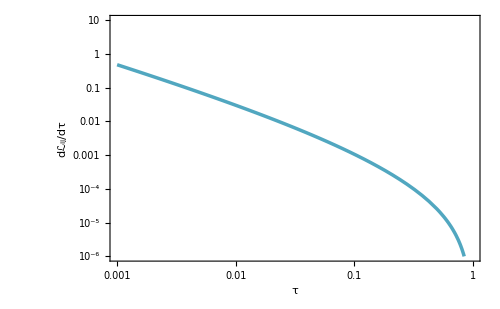

```mathematica
partonlumiwaplot=LogLogPlot[partonlumiwa[s*10^8],{s,1*10^-3,1*10^0},PlotRange->{{10^-3,1},{10^-6,10^1}},Frame->True,FrameTicks->{{tickll,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,18,FontFamily->"Times"],FrameLabel->{Style["τ",Black,18,FontFamily->"Times"],Style["dℒ_ij/dτ",Black,18,FontFamily->"Times"]},PlotStyle->{ColorData[24][5],Thickness[0.005]},ImageSize->500]
```

```mathematica
verticalline={{0.01,100},{0.01,10^-10}};
```

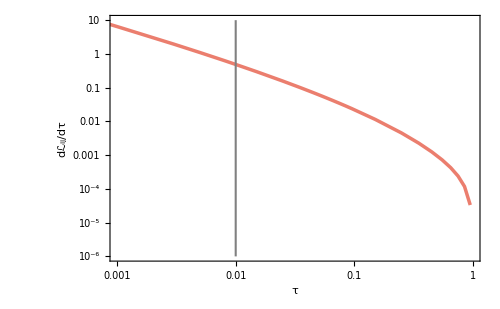

```mathematica
partonlumiaaplot=ListLogLogPlot[{partonlumiaadata,verticalline},Joined->True,PlotRange->{{10^-3,10^0},{10^-6,10^1}},PlotStyle->{{ColorData[24][1](*,Dashed*),Thickness[0.005]},{Gray(*,Dashed*),Thickness[0.003]}},Frame->True,FrameTicks->{{tickll,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,18,FontFamily->"Times"],FrameLabel->{Style["τ",Black,18,FontFamily->"Times"],Style["dℒ_ij/dτ",Black,18,FontFamily->"Times"]},ImageSize->500]
```

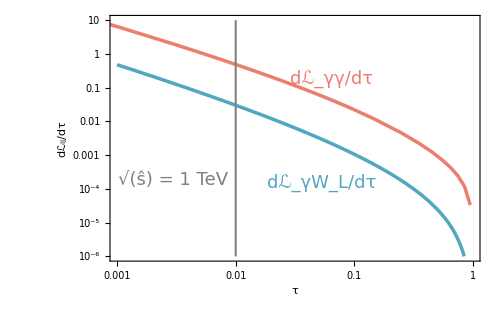

```mathematica
Show[partonlumiwaplot,partonlumiaaplot,Epilog->{Text[Style["dℒ_γγ/dτ",ColorData[24][1],18,FontFamily->"Times"],Scaled[{0.71,0.74}],Right,{1,0}],Text[Style["dℒ_γW_L/dτ",ColorData[24][5],18,FontFamily->"Times"],Scaled[{0.72,0.32}],Right,{1,0}],Text[Style["√(ŝ) = 1 TeV",Gray,18,FontFamily->"Times"],Scaled[{0.32,0.33}],Right,{1,0}]}]
```

## Plot for partonic xs, parton-lumi, partonic xs * parton-lumi

```mathematica
g1=0.350;g2=0.652;e=0.313;sinthetaw=Sqrt[0.231];costhetaw=Sqrt[1-0.231];
α1=g1^2/(4Pi);α2=g2^2/(4Pi);αs=0.118;
CB=α1/(8Pi);CW=α2/(8Pi);Cgamma=sinthetaw^2*CW+costhetaw^2*CB;
mw=80;mz=91;
fa=10000;ma=1000;gamma=1.45*10^-4;(*E0=1000;*)
Ea[E0_]:=(4*E0^2+ma^2-mw^2)/(4*E0);Ew[E0_]:=2*E0-Ea[E0];
```

```mathematica
M4[E0_,θ_]:=-(2*Sqrt[2])/fa CW*(*g2*)e*(E0*Ew[E0](Ea[E0]+Ew[E0] (1-mw^2/(Ew[E0])^2)))/mw^2*Sin[θ];
MgammaZ[E0_,θ_]:=-(8Sqrt[2])/fa  (E0^3*(Ew[E0])^2)/mw^2*Sin[θ]*((Cgamma*e*(1-Cos[θ]))/((2*E0^2-ma^2/2-mw^2/2)(1-Sqrt[1-(4*ma^2*mw^2)/((4*E0^2-ma^2-mw^2)^2)]Cos[θ]))+((CW-CB)*e*costhetaw^2*(1-Cos[θ]))/((2*E0^2-ma^2/2-mw^2/2)(1-Sqrt[1-(4*ma^2*mw^2)/((4*E0^2-ma^2-mw^2)^2)]Cos[θ])+mz^2));
Mtot[E0_,θ_]:=M4[E0,θ]-(*+*)MgammaZ[E0,θ];
```

```mathematica
integralMsquare[E0_]:=(2*Pi)*NIntegrate[((Mtot[E0,θ])^2*Sin[θ]),{θ,0,Pi}];
xs[E0_]:=1/(4*E0^2)*1/2*1/(2*(2*Pi)^2)1/4*integralMsquare[E0]*0.389379*10^9(*change GeV^-2 to pb*)
vbfxs[s_]:=(2*s^3)/(ma^5*gamma)*2^2/fa^2*(1/(128*8*Pi))^2*((ma*gamma)^2/4)/(((s-ma^2)/2)^2+(ma*gamma)^2/4)*0.389379*10^9;
```

```mathematica
xs[(5.5*10^7/4)^(1/2)]
```

9.29467×10^-8

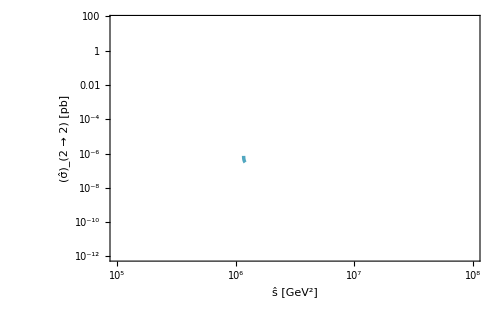

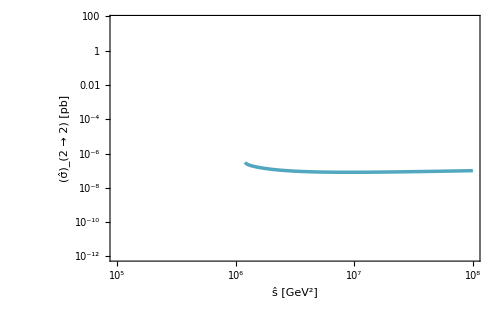

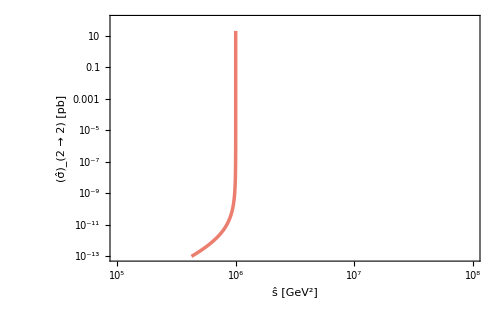

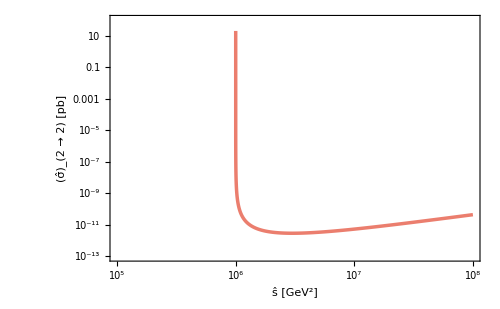

```mathematica
vbsxszeroplot=LogLogPlot[xs[Sqrt[s/4]],{s,(*1.1*10^6*)mz^2+ma^2+1,1.2*10^6},PlotRange->{{10^5,1*10^8},{10^-12,60}},Frame->True,FrameTicks->{{Automatic,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,18,FontFamily->"Times"],FrameLabel->{Style["ŝ [GeV^2]",Black,18,FontFamily->"Times"],Style["(σ̂)_(2 → 2) [pb]",Black,18,FontFamily->"Times"]},PlotStyle->{ColorData[24][5],Thickness[0.005]}]
vbsxsplot=LogLogPlot[xs[Sqrt[s/4]],{s,1.2*10^6,10^8},PlotRange->{{10^5,1*10^8},{10^-12,60}},Frame->True,FrameTicks->{{Automatic,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,18,FontFamily->"Times"],FrameLabel->{Style["ŝ [GeV^2]",Black,18,FontFamily->"Times"],Style["(σ̂)_(2 → 2) [pb]",Black,18,FontFamily->"Times"]},PlotStyle->{ColorData[24][5],Thickness[0.005]},ImageSize->500]
vbfxslowerplot=LogLogPlot[vbfxs[s],{s,10^5,10^6},PlotRange->{{10^5,10^8},{10^-13,100}},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotPoints->1000,MaxRecursion->4,FrameTicksStyle->Directive[Black,18,FontFamily->"Times"],FrameLabel->{Style["ŝ [GeV^2]",Black,18,FontFamily->"Times"],Style["(σ̂)_(2 → 2) [pb]",Black,18,FontFamily->"Times"]},PlotStyle->{ColorData[24][1],Thickness[0.005]},ImageSize->500]
vbfxsplot=LogLogPlot[vbfxs[s],{s,10^6,10^8},PlotRange->{{1*10^5,10^8},{10^-13,100}},Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotPoints->1000,MaxRecursion->4,FrameTicksStyle->Directive[Black,18,FontFamily->"Times"],FrameLabel->{Style["ŝ [GeV^2]",Black,18,FontFamily->"Times"],Style["(σ̂)_(2 → 2) [pb]",Black,18,FontFamily->"Times"]},PlotStyle->{ColorData[24][1],Thickness[0.005]},ImageSize->500]
```

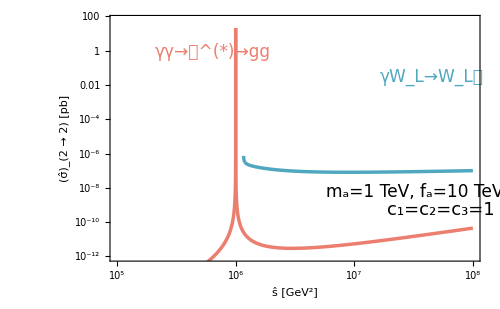

```mathematica
Show[vbsxsplot,vbsxszeroplot,vbfxslowerplot,vbfxsplot,Epilog->{Text[Style["c_1=c_2=c_3=1",Black,18,FontFamily->"Times"],Scaled[{0.75,0.21}],Left,{1,0}],Text[Style["m_a=1 TeV, f_a=10 TeV",Black,17,FontFamily->"Times"],Scaled[{0.585,0.28}],Left,{1,0}],Text[Style["γγ→(|01d44e)^(*)→gg",ColorData[24][1],17,FontFamily->"Times"],Scaled[{0.12,0.85}],Left,{1,0}],Text[Style["γW_L→W_L𝑎",ColorData[24][5],17,FontFamily->"Times"],Scaled[{0.73,0.75}],Left,{1,0}]}]
```

```mathematica
partonlumiaafunction=Exp@*Interpolation[Log@Table[{shat2[[i]],partonlumiaalist[[i]]},{i,1,Length[shat2]}]]@*Log
```

Exp@*InterpolatingFunction[…]@*Log

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {θ} = {0.0901726} 处的 θ 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.59931×10^-15 和 4.94444×10^-17.

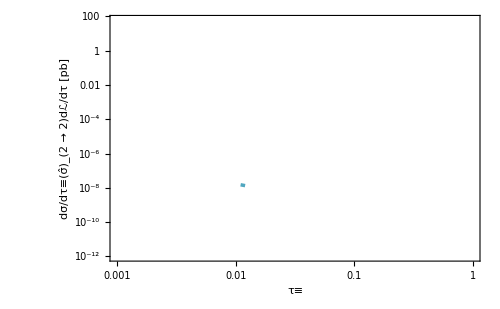

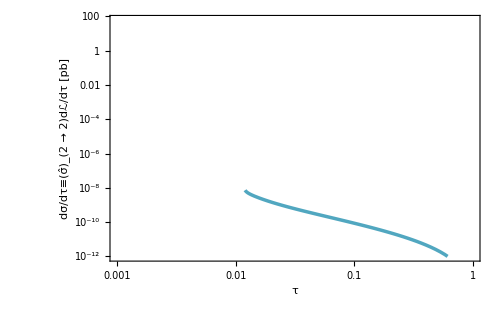

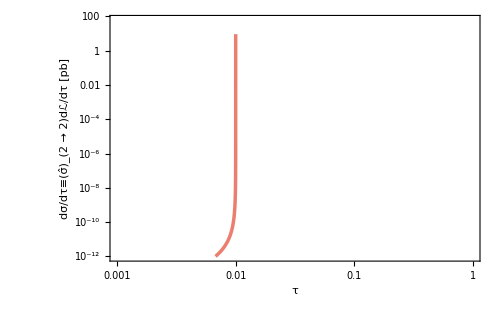

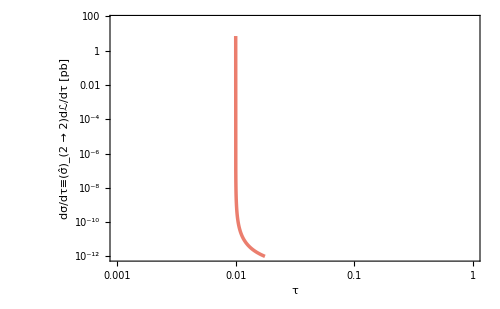

```mathematica
vbslowerplot=LogLogPlot[xs[Sqrt[s/4]]*partonlumiwa[s*10^8],{s,1.1*10^6(*(mz^2+ma^2+1)*)/10^8,1.2*10^6/10^8},PlotRange->{{1*10^5/10^8,1*10^8/10^8},{10^-12,60}},Frame->True,FrameTicks->{{Automatic,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,18,FontFamily->"Times"],FrameLabel->{Style["τ≡",Black,18,FontFamily->"Times"],Style["dσ/dτ≡(σ̂)_(2 → 2)dℒ/dτ [pb]",Black,18,FontFamily->"Times"]},PlotStyle->{ColorData[24][5],Thickness[0.005]},ImageSize->500]
vbsplot=LogLogPlot[xs[Sqrt[s*10^8/4]]*partonlumiwa[s*10^8],{s,1.2*10^6/10^8,10^8/10^8},PlotRange->{{1*10^5/10^8,1*10^8/10^8},{10^-12,60}},Frame->True,FrameTicks->{{Automatic,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,18,FontFamily->"Times"],FrameLabel->{Style["τ",Black,18,FontFamily->"Times"],Style["dσ/dτ≡(σ̂)_(2 → 2)dℒ/dτ [pb]",Black,18,FontFamily->"Times"]},PlotStyle->{ColorData[24][5],Thickness[0.005]},ImageSize->500]
vbflowerplot=LogLogPlot[vbfxs[s*10^8]*partonlumiaafunction[s*10^8],{s,10^5/10^8,10^6/10^8},PlotRange->{{1*10^5/10^8,1*10^8/10^8},{10^-12,60}},Frame->True,FrameTicks->{{Automatic,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,18,FontFamily->"Times"],FrameLabel->{Style["τ",Black,18,FontFamily->"Times"],Style["dσ/dτ≡(σ̂)_(2 → 2)dℒ/dτ [pb]",Black,18,FontFamily->"Times"]},PlotStyle->{ColorData[24][1],Thickness[0.005]},ImageSize->500]
vbfplot=LogLogPlot[vbfxs[s*10^8]*partonlumiaafunction[s*10^8],{s,10^6/10^8,10^8/10^8},PlotRange->{{1*10^5/10^8,1*10^8/10^8},{10^-12,60}},Frame->True,FrameTicks->{{Automatic,Automatic},{tickll,Automatic}},FrameTicksStyle->Directive[Black,18,FontFamily->"Times"],FrameLabel->{Style["τ",Black,18,FontFamily->"Times"],Style["dσ/dτ≡(σ̂)_(2 → 2)dℒ/dτ [pb]",Black,18,FontFamily->"Times"]},PlotStyle->{ColorData[24][1],Thickness[0.005]},ImageSize->500]
```

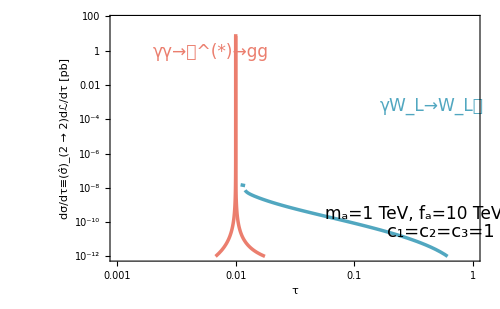

```mathematica
Show[vbsplot,vbslowerplot,vbflowerplot,vbfplot,Epilog->{Text[Style["c_1=c_2=c_3=1",Black,18,FontFamily->"Times"],Scaled[{0.75,0.12}],Left,{1,0}],Text[Style["m_a=1 TeV, f_a=10 TeV",Black,17,FontFamily->"Times"],Scaled[{0.58,0.19}],Left,{1,0}],Text[Style["γγ→(|01d44e)^(*)→gg",ColorData[24][1],17,FontFamily->"Times"],Scaled[{0.115,0.85}],Left,{1,0}],Text[Style["γW_L→W_L𝑎",ColorData[24][5],17,FontFamily->"Times"],Scaled[{0.73,0.63}],Left,{1,0}]}]
```

### let the vertical axis scientific expressed but no decimal point

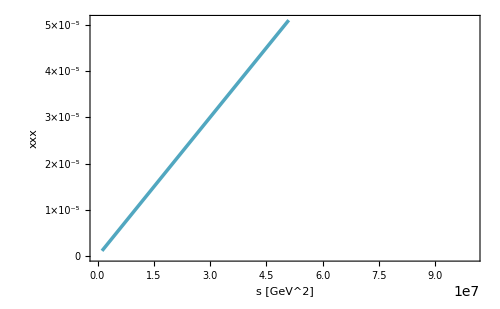

-Graphics-

```mathematica
Plot[10^-12*x,{x,1.2*10^6,10^8},PlotRange->{{0,1*10^8},{0,5.1*10^-5}},Frame->True,FrameTicks->{{Table[{y,ScientificForm[y,NumberPoint->""]},{y,0,0.00005,0.00001}],Automatic},{Automatic,Automatic}},FrameTicksStyle->Directive[Black,18,FontFamily->"Times"],FrameLabel->{Style["s [GeV^2]",Black,18,FontFamily->"Times"],Style["xxx",Black,18,FontFamily->"Times"]},PlotStyle->{ColorData[24][5],Thickness[0.005]},ImageSize->500]

Plot[10^-12*x,{x,1.2*10^6,10^8},PlotRange->{{0,1*10^8},{0,5.1*10^-5}},Frame->True,FrameTicks->{{Table[{0.00001*y,If[y==0,y,ToString[y]<>"×\!\(\*SuperscriptBox[\(10\), \(-5\)]\)"]},{y,0,5,1}],Automatic},{Automatic,Automatic}},FrameTicksStyle->Directive[Black,18,FontFamily->"Times"],FrameLabel->{Style["s [GeV^2]",Black,18,FontFamily->"Times"],Style["xxx",Black,18,FontFamily->"Times"]},PlotStyle->{ColorData[24][5],Thickness[0.005]},ImageSize->500]
```

```mathematica
Table[{s,xs[Sqrt[s/4]]},{s,1.2*10^6,}]
```

```mathematica
totalxs=NIntegrate[xs[Sqrt[s/4]]*partonlumiwa[s],{s,1.2*10^6,10^8}]/10^8
```

General::stop: 在本次计算中，NIntegrate::inumr 的进一步输出将被抑制.

0.0000228843

```mathematica
tickTop=tickll;
Do[tickTop=(tickTop/.{tickTop[[i,1]]->tickTop[[i,1]]/10^8}),{i,1,Length[tickll]}]
```

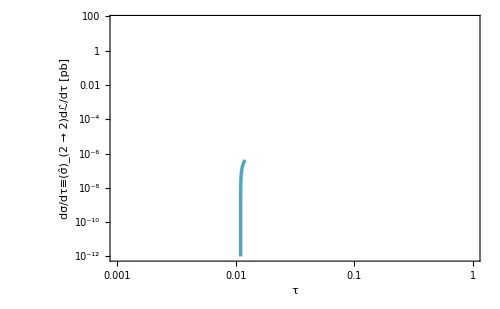

```mathematica
vbslowerplot=LogLogPlot[(1.75/0.1*10^-11*s*10^8-1.75/0.1*1.1*10^-5)*partonlumiwa[s*10^8],{s,1.1*10^6/10^8,1.2*10^6/10^8},PlotRange->{{1*10^5/10^8,1*10^8/10^8},{10^-12,60}},Frame->True,FrameTicks->{{Automatic,Automatic},{tickll,tickTop}},FrameTicksStyle->Directive[Black,18,FontFamily->"Times"],FrameLabel->{{Style["dσ/dτ≡(σ̂)_(2 → 2)dℒ/dτ [pb]",Black,18,FontFamily->"Times"],""},{Style["τ",Black,18,FontFamily->"Times"],Style["ŝ [GeV^2]",Black,18,FontFamily->"Times"]}},PlotStyle->{ColorData[24][5],Thickness[0.005]},ImageSize->500]
```